## Generates heat-map showing the refractory zone with variation in distortion probability and fertility fitness of heterozygotes

#### Module:

```mathematica
(* Clear eariler stored variables/constants*)
Clear["Global`*"]  

(* arearelease[] module takes f_WD, p as input and returns the Area of refractory zone as output*)
arearelease[ffwdin_,pin_,din_,sin_]:=Module[{ffwd0=ffwdin,p0=pin,d0=din,s0=sin},
xwd[xww_,xdd_] := 1-xww-xdd;
fww [xww_,xdd_,ffww_,ffwd_,ffdd_,p_,d_,e_]:= (ffww*ffww xww xww + (1-p)(1-e/2)*ffww*ffwd xww xwd[xww,xdd] +(1-d)(1-e/2)(1-p)*ffww*ffwd xww xwd[xww,xdd]+ (1-d)(1-p)^2 ffwd*ffwd xwd[xww,xdd] xwd[xww,xdd]);
fdd[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ν_,s_] := ν(1-s)(ffdd*ffdd xdd xdd+ 2 p ffdd*ffwd xdd xwd[xww,xdd]+ p^2ffwd*ffwd xwd[xww,xdd]xwd[xww,xdd]); 
fwd[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ω_,h_,s_,e_] := (1-h s)*ω(2 p (1-p)ffwd*ffwd xwd[xww,xdd] xwd[xww,xdd]+ 2(1-p)ffdd*ffwd xdd xwd[xww,xdd]+2 (1-e/2) p ffww*ffwd xww xwd[xww,xdd]+(2-e)*ffdd*ffww xdd xww)-Ceiling[h]*Ceiling[s]*(1-h*s)*ω(ffdd*ffww xdd xww+p ffww*ffwd xww xwd[xww,xdd]); 
ftot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ν_,ω_,d_,h_,s_,e_]:= fww[xww,xdd,ffww,ffwd,ffdd,p,d,e]+fwd[xww,xdd,ffww,ffwd,ffdd,p,ω,h,s,e]+fdd[xww,xdd,ffww,ffwd,ffdd,p,ν,s];
xdot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ν_,ω_,d_,h_,s_,e_] := fww[xww,xdd,ffww,ffwd,ffdd,p,d,e]-xww*ftot[xww,xdd,ffww,ffwd,ffdd,p,ν,ω,d,h,s,e]; 
ydot[xww_,xdd_,ffww_,ffwd_,ffdd_,p_,ν_,ω_,d_,h_,s_,e_] := fdd[xww,xdd,ffww,ffwd,ffdd,p,ν,s]-xdd*ftot[xww,xdd,ffww,ffwd,ffdd,p,ν,ω,d,h,s,e]; 

(* Coordinates of the triangle containing the phase space (de Finetti diagram)*)
x1 = 0; y1 = 0;
x3 = 0.5; y3 = Sqrt[3]/2.;
x2 = 1; y2 = 0;

(* Transforamtion from barycentric to Cartesian *)
xncart[x_,y_] := x1 x+x2 y + x3 (1-x-y);
yncart[x_,y_] := y1 x+y2 y + y3 (1-x-y);
lamda1[xcart_,ycart_]:= ((y2-y3)(xcart-x3)+(x3-x2)(ycart-y3))/((y2-y3)(x1-x3)+(x3-x2)(y1-y3));
lamda2[xcart_,ycart_]:= ((y3-y1)*(xcart-x3)+(x1-x3)(ycart-y3))/((y2-y3)(x1-x3)+(x3-x2)(y1-y3));
xdotcart[xcart_,ycart_,ffww_,ffwd_,ffdd_,p_,ν_,ω_,d_,h_,s_,e_]:=(x1-x3)*xdot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,ν,ω,d,h,s,e]+(x2-x3)*ydot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,ν,ω,d,h,s,e];
ydotcart[xcart_,ycart_,ffww_,ffwd_,ffdd_,p_,ν_,ω_,d_,h_,s_,e_]:=(y1-y3)*xdot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,ν,ω,d,h,s,e]+(y2-y3)*ydot[lamda1[xcart,ycart],lamda2[xcart,ycart],ffww,ffwd,ffdd,p,ν,ω,d,h,s,e];

ffww0=1; ffdd0=1; ν0=1; ω0=1; h0=0.9; e0=0;
polyn1 = Expand[xdot[x,a0 + a1 x+a2 x^2  ,ffww0,ffwd0,ffdd0,p0,ν0,ω0,d0,h0,s0,e0]*D[a0 + a1 x  ,x]];
polyn2 = Expand[ydot[x,a0 + a1 x +a2 x^2 ,ffww0,ffwd0,ffdd0,p0,ν0,ω0,d0,h0,s0,e0]];

sol1 =Quiet[Solve[Thread[Equal[Coefficient[polyn1,x,#]&/@Range[0,2],Coefficient[polyn2,x,#]&/@Range[0,2]]]]];
If[Length[sol1]≥ 1,solution ="yes",solution ="no"];
If[solution =="no",
Area1=0
];

If[solution =="yes"(*&& Length[sol1]!= 7*),
soln=Ceiling[(Length[sol1]+1)/2];
separatrix2[x_,y_] :=(a0 + a1 x )/.sol1⟦soln⟧;
Subscript[ℛ, triangle]=ImplicitRegion[ycart - Sqrt[3]*xcart ≤    0 && ycart + Sqrt[3]*xcart- Sqrt[3]≤  0 && ycart≥  0 ,{xcart,ycart}];
Subscript[ℛ, separatrix]=ImplicitRegion[separatrix2[lamda1[xcart,ycart],lamda2[xcart,ycart]]-lamda2[xcart,ycart] >   0 ,{xcart,ycart}];
Subscript[ℛ, int]=RegionIntersection[ Subscript[ℛ, triangle],Subscript[ℛ, separatrix]];
Area1 =Chop[Area[Subscript[ℛ, int]]/(Sqrt[3]/4 )];
];
Area1
]
```

#### Output:

```mathematica
(* Generates Data table *)
data1=Table[{pvar,fwdvar,arearelease[fwdvar,pvar,0,0]},{fwdvar,0.0,0.95,0.05},{pvar,0.50,1.0,0.05}]; 

heatmap1 = ListDensityPlot[Flatten[data1,1],Mesh->None,ColorFunctionScaling->True,ColorFunction->"SunsetColors",PlotLegends->Automatic,Frame->True,FrameStyle->Thickness[0.003],PlotRange->Automatic,ImagePadding->20];
```

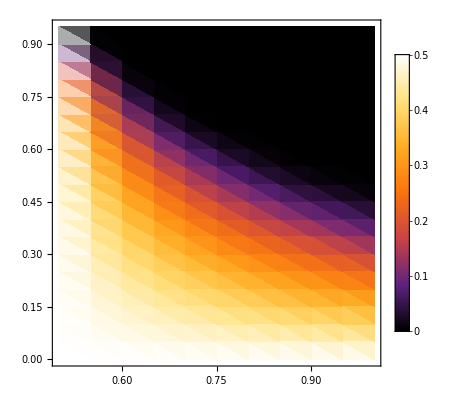

```mathematica
heatmap1
```